# Homework 5

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

```mathematica
ClearAll["Global`*"]
```

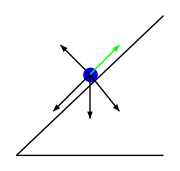

```mathematica
(*For Uphill and Downhill motion, assuming that the only acting force that does work on the moving object is gravity*)
(*I will consider the hill to have a constant slope with an angle θ along the the path of motion of the object*)

ClearAll["Global`*"]
g1=Graphics[{Black,Line[{{0,0},{20,19}}]}];
g2=Graphics[{Black,Line[{{0,0},{20,0}}]}];
g3=Graphics[{Blue,Disk[{10,11}]}];
g4=Graphics[Arrow[{{10,11},{10,5}}]];                                             (*The free body diagram for uphill motion*)      
g5=Graphics[Arrow[{{10,11},{5,6}}]];
g6=Graphics[Arrow[{{10,11},{14,6}}]];
g7=Graphics[Arrow[{{10,11},{6,15}}]];
g8=Graphics[{Green,Arrow[{{10,11},{14,15}}]}];(*The direction of motion*)
Show[{g1,g2,g3,g4,g5,g6,g7,g8},ImageSize->Small]
```

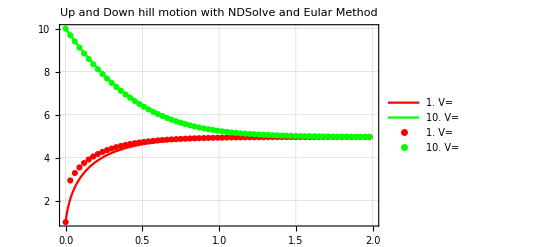

```mathematica
ClearAll["Global`*"]
g=9.81; θ=π/180 10;
power=4000.0; m=50.0;
c=1.4; ρ=1.0152; A=2.0;
color={Red,Green,Blue,Purple};

tstart=0; tend=2; dt=0.03; 
Subscript[μ, k]=1.42; (*Kinetic Friction of the road*)
tlist=Range[tstart,tend,dt]; lt=Length[tlist];
vlist=0 tlist;

hinitial=0;velinitial={1.0,10.0}; lvelinitial=Length[velinitial];
eularlistfig=0 velinitial; leularlistfig=Length[eularlistfig];
numlistfig=0 velinitial; lnumlistfig=Length[numlistfig];


(*Using NDsolve to solve for the equation of motion*)
(*The EoM is: (d^2 h)/dt^2=-g sin(θ)-g cos(θ) Subscript[μ, k] *)

(*For Uphill and Downhill Motion*)
Do[numsol=NDSolve[{vel'[t]==power/(m vel[t])-(c ρ A vel[t]^2)/(2 m)-g (Sin[θ]+Subscript[μ, k] Cos[θ]),vel[tstart]==velinitial[[i]]},vel[t],{t,tstart,tend}];
numlistfig[[i]]=Plot[Evaluate[vel[t]/.numsol],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"V= " velinitial[[i]]},Right],PlotStyle->{color[[i]],Thick}],{i,1,lnumlistfig}];


(*Solving the EoM using eular's method:*)

Do[vlist[[1]]=velinitial[[j]];
Do[vlist[[i]]=vlist[[i-1]]+dt (power/(m vlist[[i-1]])-(c ρ A vlist[[i-1]]^2)/(2 m)-g (Sin[θ]+Subscript[μ, k] Cos[θ])),{i,2,lt}];eularlistfig[[j]]=ListPlot[Table[{tlist[[k]],vlist[[k]]},{k,1,lt}],PlotRange->All,PlotLegends->Placed[{"V= " velinitial[[j]]},Right],PlotStyle->color[[j]]],{j,1,lvelinitial}];

Show[{numlistfig[[1]],numlistfig[[2]],eularlistfig[[1]],eularlistfig[[2]]},PlotRange->All,PlotLabel-> "Up and Down hill motion with NDSolve and Eular Method",Frame->True,GridLines->Automatic]
```

## Problem 2

```mathematica
(*The basic equations of motion for a moving baseball including the air drag effects are:
Subscript[dv, x]/dt=(-Subscript[B, 2])/m Subscript[v, x] v , Subscript[dv, y]/dt=-g-Subscript[b, 2]/m Subscript[v, y] v , dx/dt=Subscript[v, x], dy/dt=Subscript[v, y]*)
(*The new equations of motion for a moving baseball including the air drag effects and the effect of the wind are:
Subscript[dv, x]/dt=(-Subscript[B, 2])/m(Subscript[v, x]-Subscript[v, wind,x])|v-Subscript[v, wind]| , Subscript[dv, y]/dt=-g-Subscript[b, 2]/m(Subscript[v, y]-Subscript[v, wind,y])|v-Subscript[v, wind]| , dx/dt=Subscript[v, x], dy/dt=Subscript[v, y]*)
```

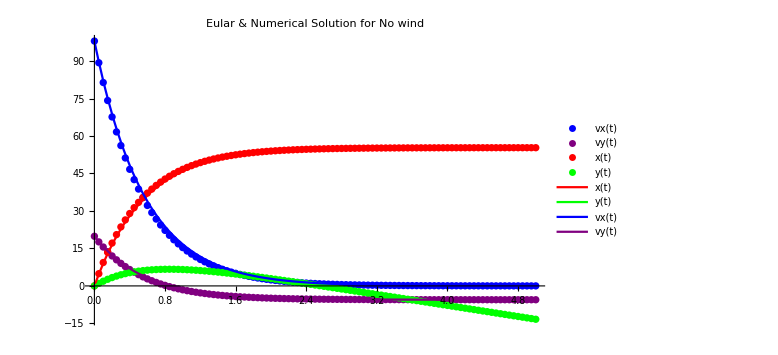

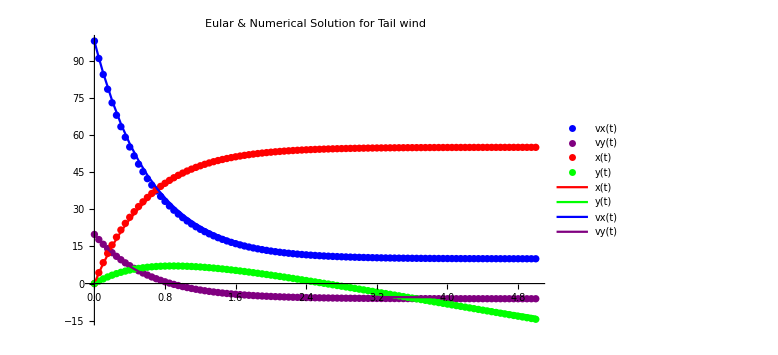

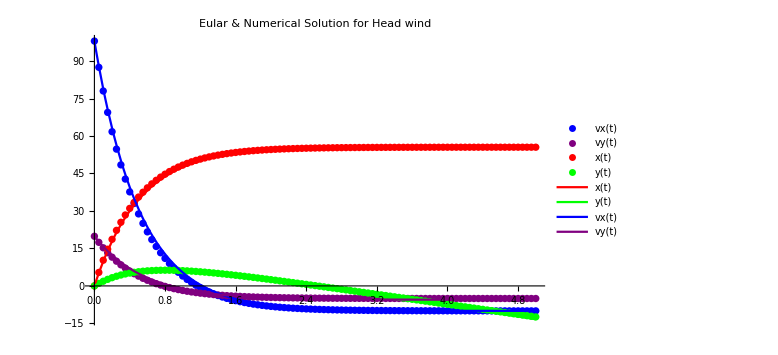

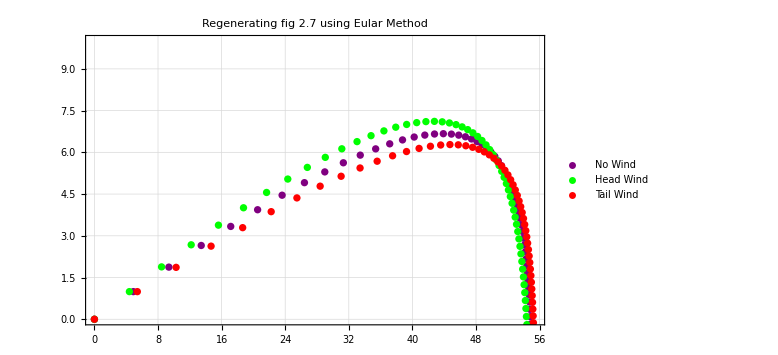

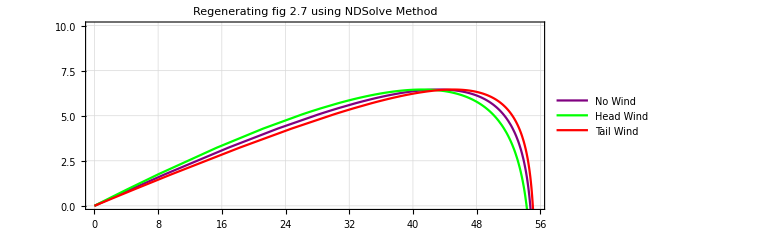

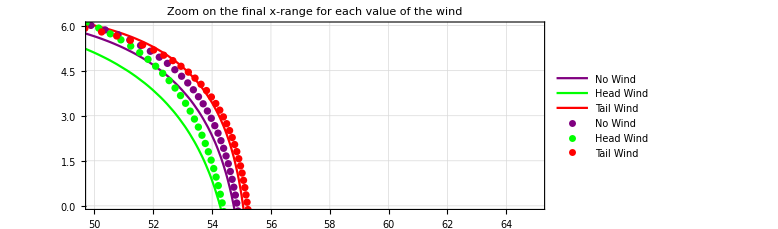

```mathematica
ClearAll["Global`*"]

m=70;  g=9.81; Subscript[B, 2]=1.24;
Subscript[v, wind]={0,10,-10}; Subscript[lv, wind]=Length[Subscript[v, wind]]; (*All entries here are supposed to be in x-direction. However, extension to wind in any arbitrary direction is easy*)
initialv=100;linitialv=Length[initialv]; initialx=0;initialy=0;
θ=0.2; (*The angle with which the ball is batted*)
eularlistfig=0 Subscript[v, wind]; leularlistfig=Length[eularlistfig];

color={Red,Green,Blue,Purple};

tstart=0; tend=5; dt=0.05;
tlist=Range[tstart,tend,dt]; lt=Length[tlist];
xlist=0 tlist; ylist=0 tlist; vxlist=0 tlist;vylist=0 tlist;
eularlistfig=0 Subscript[v, wind]; leularlistfig=Length[eularlistfig];

(*Solving the new system using NDSolve:*)

numsol=0 Subscript[v, wind]; lnumsol=Length[numsol];

Do[numsol[[i]]=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2])/m(vx[t]-Subscript[v, wind][[i]]) (initialv-Subscript[v, wind][[i]]),vy'[t]==-g-Subscript[B, 2]/m vy[t] initialv,x'[t]==vx[t]-Subscript[v, wind][[i]],y'[t]==vy[t],vx[tstart]==initialv Cos[θ],vy[tstart]==initialv Sin[θ],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]],{i,1,lnumsol}];


vxfig11=Plot[Evaluate[vx[t]/.numsol[[1]][[1]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig11=Plot[Evaluate[vy[t]/.numsol[[1]][[2]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];
xfig11=Plot[Evaluate[x[t]/.numsol[[1]][[3]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig11=Plot[Evaluate[y[t]/.numsol[[1]][[4]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];

vxfig22=Plot[Evaluate[vx[t]/.numsol[[2]][[1]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig22=Plot[Evaluate[vy[t]/.numsol[[2]][[2]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];
xfig22=Plot[Evaluate[x[t]/.numsol[[2]][[3]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig22=Plot[Evaluate[y[t]/.numsol[[2]][[4]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];

(*Show[{vxfig,vyfig,xfig,yfig},PlotLabel->"Numerical Solution for Tail wind",ImageSize->Large]*)

vxfig33=Plot[Evaluate[vx[t]/.numsol[[3]][[1]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig33=Plot[Evaluate[vy[t]/.numsol[[3]][[2]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];
xfig33=Plot[Evaluate[x[t]/.numsol[[3]][[3]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig33=Plot[Evaluate[y[t]/.numsol[[3]][[4]]],{t,tstart,tend},PlotRange->All,PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];

(*Show[{vxfig,vyfig,xfig,yfig},PlotLabel->"Numerical Solution for Head wind",ImageSize->Large]*)


(*Solution Using Eular's Method*)

xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ]; vylist[[1]]=initialv Sin[θ];


(*For No wind*)

Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]-Subscript[v, wind][[1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] (initialv) (vxlist[[i-1]]-Subscript[v, wind][[1]]))/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] initialv (vylist[[i-1]]))/m) dt,{i,2,lt}];
xfig1=ListPlot[{Table[{tlist[[k]],xlist[[k]]},{k,lt}]},PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig1=ListPlot[{Table[{tlist[[k]],ylist[[k]]},{k,lt}]},PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];
vxfig1=ListPlot[{Table[{tlist[[k]],vxlist[[k]]},{k,lt}]},PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig1=ListPlot[{Table[{tlist[[k]],vylist[[k]]},{k,lt}]},PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];

p1eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,lt}]},PlotStyle->{Purple,Dashed},PlotLegends->Placed[{"No Wind"},Right]];


(*For Head wind*)

(*effective speed*) vtrue=Sqrt[((initialv Cos[θ])-Subscript[v, wind][[2]])^2+(initialv Sin[θ])^2];
Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]-Subscript[v, wind][[2]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] vtrue (vxlist[[i-1]]-Subscript[v, wind][[2]]))/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] vtrue (vylist[[i-1]]))/m) dt,{i,2,lt}];
xfig2=ListPlot[{Table[{tlist[[k]],xlist[[k]]},{k,lt}]},PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig2=ListPlot[{Table[{tlist[[k]],ylist[[k]]},{k,lt}]},PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];
vxfig2=ListPlot[{Table[{tlist[[k]],vxlist[[k]]},{k,lt}]},PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig2=ListPlot[{Table[{tlist[[k]],vylist[[k]]},{k,lt}]},PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];

p2eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,lt}]},PlotStyle->{Green,Dashed},PlotLegends->Placed[{"Head Wind"},Right]];


(*For Tail wind*)

(*effective speed*) vtrue=Sqrt[((initialv Cos[θ])-Subscript[v, wind][[3]])^2+(initialv Sin[θ])^2];
Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]-Subscript[v, wind][[3]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] vtrue (vxlist[[i-1]]-Subscript[v, wind][[3]]))/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] vtrue (vylist[[i-1]]))/m) dt,{i,2,lt}];
xfig3=ListPlot[{Table[{tlist[[k]],xlist[[k]]},{k,lt}]},PlotLegends->Placed[{"x(t)"},Right],PlotStyle-> {color[[1]]}];
yfig3=ListPlot[{Table[{tlist[[k]],ylist[[k]]},{k,lt}]},PlotLegends->Placed[{"y(t)"},Right],PlotStyle-> {color[[2]]}];
vxfig3=ListPlot[{Table[{tlist[[k]],vxlist[[k]]},{k,lt}]},PlotLegends->Placed[{"vx(t)"},Right],PlotStyle-> {color[[3]]}];
vyfig3=ListPlot[{Table[{tlist[[k]],vylist[[k]]},{k,lt}]},PlotLegends->Placed[{"vy(t)"},Right],PlotStyle-> {color[[4]]}];

p3eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,lt}]},PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Tail Wind"},Right]];


Show[{vxfig1,vyfig1,xfig1,yfig1,xfig11,yfig11,vxfig11,vyfig11},PlotLabel->"Eular & Numerical Solution for No wind",ImageSize->Large,PlotRange->All]

Show[{vxfig2,vyfig2,xfig2,yfig2,xfig22,yfig22,vxfig22,vyfig22},PlotLabel->"Eular & Numerical Solution for Tail wind",ImageSize->Large,PlotRange->All]

Show[{vxfig3,vyfig3,xfig3,yfig3,xfig33,yfig33,vxfig33,vyfig33},PlotLabel->"Eular & Numerical Solution for Head wind",ImageSize->Large,PlotRange->All]


p1num=ParametricPlot[{Evaluate[x[t]/.numsol[[1]][[3]]],Evaluate[y[t]/.numsol[[1]][[4]]]},{t,tstart,tend},PlotStyle->{Purple,Thick},PlotLegends->Placed[{"No Wind"},Right]];
p2num=ParametricPlot[{Evaluate[x[t]/.numsol[[2]][[3]]],Evaluate[y[t]/.numsol[[2]][[4]]]},{t,tstart,tend},PlotStyle->{Green,Thick},PlotLegends->Placed[{"Head Wind"},Right]];
p3num=ParametricPlot[{Evaluate[x[t]/.numsol[[3]][[3]]],Evaluate[y[t]/.numsol[[3]][[4]]]},{t,tstart,tend},PlotStyle->{Red,Thick},PlotLegends->Placed[{"Tail Wind"},Right]];


Show[{p1eular,p2eular,p3eular},AxesOrigin->{0,0},PlotRange->{0,10},ImageSize->Large,PlotLabel->"Regenerating fig 2.7 using Eular Method",Frame-> True,GridLines-> Automatic]

Show[{p1num,p2num,p3num},AxesOrigin->{0,0},PlotRange->{0,10},ImageSize->Large,PlotLabel->"Regenerating fig 2.7 using NDSolve Method",Frame-> True,GridLines-> Automatic]

Show[{p1num,p2num,p3num,p1eular,p2eular,p3eular},AxesOrigin->{50,0},PlotRange->{{50,65},{0,6}},ImageSize->Large,PlotLabel->"Zoom on the final x-range for each value of the wind",Frame-> True,GridLines-> Automatic]
```

## Problem 3

```mathematica
(*For the Isothermal model, Subscript[B, 2]-> Subscript[B, 2]*(ⅇ^(-y/Subscript[y, 0])), Where Subscript[y, 0] = (Subscript[K, B] T)/(m g) = 1.0*10^4. For the Adiabatic model, Subscript[B, 2]-> Subscript[B, 2]*(1-(a y)/Subscript[T, 0])^α*)
```

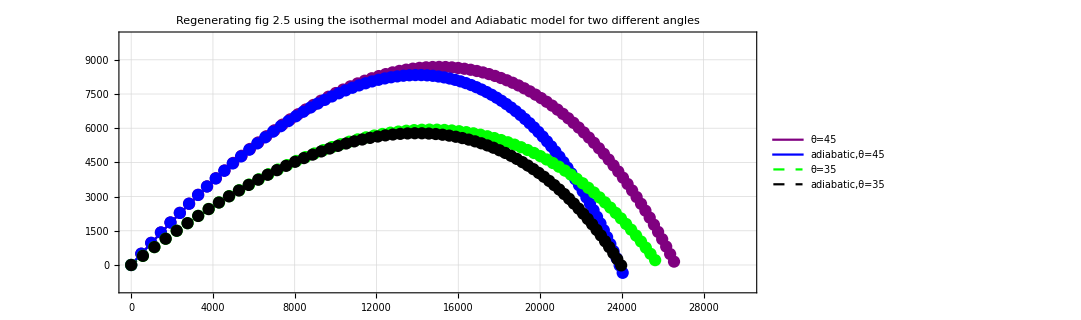

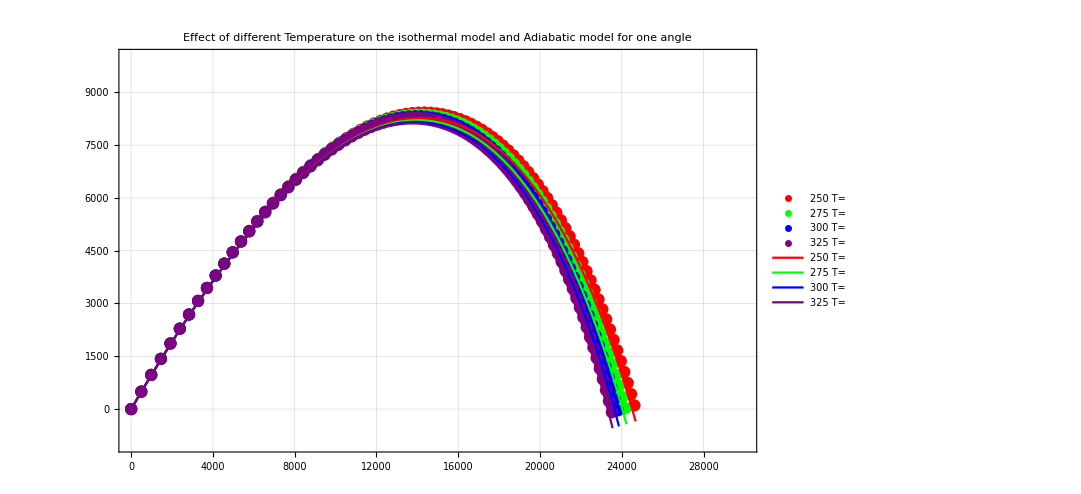

```mathematica
ClearAll["Global`*"];
m=70;  g=9.81; Subscript[B, 2]=0.002; Subscript[y, 0]=1.0 10^4; a=6.5 10^-3; α=2.5; Subscript[T, 0]=294;
initialv=700;linitialv=Length[initialv]; initialx=0;initialy=0;
θ={π/4,(35 π)/180}; (*The angle with which the ball is batted*)
eularlistfig=0 Subscript[v, wind]; leularlistfig=Length[eularlistfig];

tstart=0; tend=100; dt=1.0;
tlist=Range[tstart,tend,dt]; lt=Length[tlist];
xlist=0 tlist; ylist=0 tlist; vxlist=0 tlist;vylist=0 tlist;



(*Solving Using NDSolve*)

(*The Isothermal Model*)

sol45=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2] ⅇ^((-y[t])/Subscript[y, 0]))/m vx[t] initialv,vy'[t]==-g-(Subscript[B, 2]  ⅇ^((-y[t])/Subscript[y, 0]))/m vy[t] initialv,x'[t]==vx[t],y'[t]==vy[t],vx[tstart]==initialv Cos[θ[[1]]],vy[tstart]==initialv Sin[θ[[1]]],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]];

sol35=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2] ⅇ^((-y[t])/Subscript[y, 0]))/m vx[t] initialv,vy'[t]==-g-(Subscript[B, 2]  ⅇ^((-y[t])/Subscript[y, 0]))/m vy[t] initialv,x'[t]==vx[t],y'[t]==vy[t],vx[tstart]==initialv Cos[θ[[2]]],vy[tstart]==initialv Sin[θ[[2]]],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]];


fig45=ParametricPlot[{Evaluate[x[t]/.sol45[[3]]],Evaluate[y[t]/.sol45[[4]]]},{t,tstart,84},PlotStyle->{Purple,Thick},PlotLegends->Placed[{"θ=45"},Right]];

fig35=ParametricPlot[{Evaluate[x[t]/.sol35[[3]]],Evaluate[y[t]/.sol35[[4]]]},{t,tstart,69},PlotStyle->{Green,Dashed},PlotLegends->Placed[{"θ=35"},Right]];



(*For the Adiabatic model*)

asol45=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2] (1-(a y[t])/Subscript[T, 0])^α)/m vx[t] initialv,vy'[t]==-g-(Subscript[B, 2]   (1-(a y[t])/Subscript[T, 0])^α)/m vy[t] initialv,x'[t]==vx[t],y'[t]==vy[t],vx[tstart]==initialv Cos[θ[[1]]],vy[tstart]==initialv Sin[θ[[1]]],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]];

asol35=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2]  (1-(a y[t])/Subscript[T, 0])^α)/m vx[t] initialv,vy'[t]==-g-(Subscript[B, 2]   (1-(a y[t])/Subscript[T, 0])^α)/m vy[t] initialv,x'[t]==vx[t],y'[t]==vy[t],vx[tstart]==initialv Cos[θ[[2]]],vy[tstart]==initialv Sin[θ[[2]]],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]];

afig45=ParametricPlot[{Evaluate[x[t]/.asol45[[3]]],Evaluate[y[t]/.asol45[[4]]]},{t,tstart,84},PlotStyle->{Blue,Thick},PlotLegends->Placed[{"adiabatic,θ=45"},Right]];

afig35=ParametricPlot[{Evaluate[x[t]/.asol35[[3]]],Evaluate[y[t]/.asol35[[4]]]},{t,tstart,69},PlotStyle->{Black,Dashed},PlotLegends->Placed[{"adiabatic,θ=35"},Right]];



(*Solving Using Eular's Method*)

(*The Isothermal Model*)

xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ[[1]]]; vylist[[1]]=initialv Sin[θ[[1]]];

Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] ⅇ^((-ylist[[i-1]])/Subscript[y, 0]) (initialv) (vxlist[[i-1]]))/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] ⅇ^((-ylist[[i-1]])/Subscript[y, 0])  initialv (vylist[[i-1]]))/m) dt,{i,2,lt}];

fig45eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,85}]},PlotStyle->{Purple}];



xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ[[2]]]; vylist[[1]]=initialv Sin[θ[[2]]];

Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] ⅇ^((-ylist[[i-1]])/Subscript[y, 0]) (initialv) (vxlist[[i-1]]))/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] ⅇ^((-ylist[[i-1]])/Subscript[y, 0])  initialv (vylist[[i-1]]))/m) dt,{i,2,lt}];

fig35eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,70}]},PlotStyle->{Green}];



(*For the Adiabatic model*)

xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ[[1]]]; vylist[[1]]=initialv Sin[θ[[1]]];

Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] (1-(a ylist[[i-1]])/Subscript[T, 0])^α initialv vxlist[[i-1]])/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] (1-(a ylist[[i-1]])/Subscript[T, 0])^α initialv vylist[[i-1]])/m) dt,{i,2,lt}];

afig45eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,85}]},PlotStyle->{Blue}];

                                       

xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ[[2]]]; vylist[[1]]=initialv Sin[θ[[2]]];

Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] (1-(a ylist[[i-1]])/Subscript[T, 0])^α initialv vxlist[[i-1]])/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] (1-(a ylist[[i-1]])/Subscript[T, 0])^α initialv vylist[[i-1]])/m) dt,{i,2,lt}];

afig35eular=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,70}]},PlotStyle->{Black}];


Show[{fig45,afig45,fig35,afig35,fig45eular,afig45eular,fig35eular,afig35eular},PlotRange->{{0,30000},{-1000,10000}},AxesOrigin->{0,0},ImageSize->800,Frame-> True,GridLines->Automatic, PlotLabel-> "Regenerating fig 2.5 using the isothermal model and Adiabatic model for two different angles"]


(*For θ=π/4 and Temperature = {250,275,300,325}*)
(*For the isothermal model, the temperature variation will have no effect on the trajectory of the ball. Therefore, the solution for the isothermal case here is like the previous one*)

T={250,275,300,325}; lT=Length[T];
Tfigeular=0 T; Tfignum=0 T;
color={Red,Green,Blue,Purple};

(*The adiabatic model for θ=π/4*)

xlist[[1]]=initialx; ylist[[1]]=initialy; vxlist[[1]]=initialv Cos[θ[[1]]]; vylist[[1]]=initialv Sin[θ[[1]]];

Do[Do[xlist[[i]]=xlist[[i-1]]+(vxlist[[i-1]]) dt;vxlist[[i]]=vxlist[[i-1]]-((Subscript[B, 2] (1-(a ylist[[i-1]])/T[[j]])^α initialv vxlist[[i-1]])/m) dt;ylist[[i]]=ylist[[i-1]]+vylist[[i-1]] dt;vylist[[i]]=vylist[[i-1]]-(g+(Subscript[B, 2] (1-(a ylist[[i-1]])/T[[j]])^α initialv vylist[[i-1]])/m) dt,{i,2,lt}];Tfigeular[[j]]=ListPlot[{Table[{xlist[[k]],ylist[[k]]},{k,84}]},PlotStyle->{color[[j]]},PlotLegends->Placed[{T[[j]]" T="},Right]],{j,1,lT}];

(*Using the NDSolve*)

Do[Tsol=Flatten[NDSolve[{vx'[t]==(-Subscript[B, 2] (1-(a y[t])/T[[j]])^α)/m vx[t] initialv,vy'[t]==-g-(Subscript[B, 2]   (1-(a y[t])/T[[j]])^α)/m vy[t] initialv,x'[t]==vx[t],y'[t]==vy[t],vx[tstart]==initialv Cos[θ[[1]]],vy[tstart]==initialv Sin[θ[[1]]],x[tstart]==0,y[tstart]==0},{vx[t],vy[t],x[t],y[t]},{t,tstart,tend}]];Tfignum[[j]]=ParametricPlot[{Evaluate[x[t]/.Tsol[[3]]],Evaluate[y[t]/.Tsol[[4]]]},{t,tstart,84},PlotStyle->{color[[j]],Thick},PlotLegends->Placed[{T[[j]]" T="},Right]],{j,1,lT}];




Show[{Tfigeular[[1]],Tfigeular[[2]],Tfigeular[[3]],Tfigeular[[4]],Tfignum[[1]],Tfignum[[2]],Tfignum[[3]],Tfignum[[4]]},AxesOrigin->{0,0},PlotRange->{{0,30000},{-1000,10000}},ImageSize->800,Frame-> True,GridLines->Automatic, PlotLabel-> "Effect of different Temperature on the isothermal model and Adiabatic model for one angle"]
```